```mathematica
Gr[tuple_] := Module[{result =0, l, plus},

Return [N[magicGraham[tuple]]*Mean[Mean[Ratios[Permutations[tuple]]]]];
]
```

```mathematica
Last[N[Accumulate[Log[Differences[{3,5,7,19}]]]]]
```

3.8712

```mathematica
Gr[{3,5,7,11}]
```

-0.273022

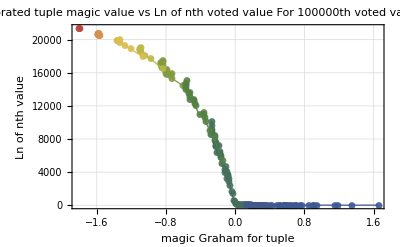

```mathematica
With[
{range = 100000},
With[
{fileName = FileNameForVotedValuesSummary[range]},
With[
{values=ReadList[fileName]},
With[
{min = Min[Map[Length[#[[1]]]&, values]],
max = Max[Map[Length[#[[1]]]&, values]]
},
Show[
Table[
ListPlot[
Sort[Table[N [{Gr[tuple[[1]]] ,Log[10,tuple[[2]]]}], {tuple, Select[values, Length[#[[1]]] == l &]}]],
AxesLabel->{"magic Graham for tuple", "Ln of nth value"},
AxesStyle->Directive[Thick, Darker[Darker[Green]],12],
AxesOrigin->{0,0},
PlotLabel->"Calibrated tuple magic value vs Ln of nth voted value\nFor " <> ToString[range]<>"th voted value\n"<> ToString[Length[values]]<>" tuples",
GridLines->Automatic,
Frame->True,
PlotMarkers->Automatic,
LabelStyle->{FontFamily->"Calibri", FontSize->Larger},
ImageSize->{1000},
PlotRange->All,
PlotStyle->Directive[Opacity[0.9], ColorData["DarkRainbow"][(l-min) / (max+1-min)]],
Joined->True
] 
,{l, min, max}
]
]
]
]
]
]
```

```mathematica
TableForm[Sort[Map[{N [Log[10,#[[2]]]],N[magicGraham[#[[1]]]],Gr[#[[1]]],#[[1]], Fold[Times,1,#[[1]]]}&,ReadList[FileNameForVotedValuesSummary[100000]]], #1[[2]]>#2[[2]]&], TableDepth->2, TableAlignments->Right,TableHeadings->{Automatic,{"Log10 voted value", "magic", "magic calibrated", "tuple", "tuple product"}}]
```

| Log10 voted value | magic | magic calibrated | tuple | tuple product
1 | 8.17471 | 0.568033 | 0.594182 | {17,23} | 391
2 | 8.17396 | 0.557535 | 0.560988 | {17,19} | 323
3 | 8.28849 | 0.551163 | 0.643331 | {13,23} | 299
4 | 8.31805 | 0.540666 | 0.580067 | {13,19} | 247
5 | 8.47401 | 0.539731 | 0.69333 | {11,23} | 253
6 | 8.28586 | 0.534178 | 0.553515 | {13,17} | 221
7 | 8.47374 | 0.529233 | 0.610264 | {11,19} | 209
8 | 8.70529 | 0.522746 | 0.573063 | {11,17} | 187
9 | 8.97457 | 0.505876 | 0.512951 | {11,13} | 143
10 | 8.79561 | 0.504923 | 0.906353 | {7,23} | 161
11 | 8.9549 | 0.494426 | 0.762085 | {7,19} | 133
12 | 8.97649 | 0.487938 | 0.692954 | {7,17} | 119
13 | 9.18405 | 0.475115 | 1.14441 | {5,23} | 115
14 | 9.42562 | 0.471069 | 0.564247 | {7,13} | 91
15 | 9.43137 | 0.464618 | 0.943907 | {5,19} | 95
16 | 9.45739 | 0.459636 | 0.507391 | {7,11} | 77
17 | 9.4088 | 0.45813 | 0.846193 | {5,17} | 85
18 | 10.1287 | 0.441261 | 0.658497 | {5,13} | 65
19 | 10.4928 | 0.429828 | 0.570499 | {5,11} | 55
20 | 10.0707 | 0.423439 | 1.6508 | {3,23} | 69
21 | 11.0203 | 0.412941 | 1.34025 | {3,19} | 57
22 | 10.5588 | 0.406454 | 1.18748 | {3,17} | 51
23 | 11.2974 | 0.395021 | 0.417593 | {5,7} | 35
24 | 10.6605 | 0.389584 | 0.889051 | {3,13} | 39
25 | 11.1145 | 0.378151 | 0.744844 | {3,11} | 33
26 | 11.9942 | 0.343344 | 0.474142 | {3,7} | 21
27 | 12.4188 | 0.31619 | 0.325668 | {13,17,19} | 4199
28 | 13.3597 | 0.313536 | 0.355341 | {3,5} | 15
29 | 13.1035 | 0.304757 | 0.324977 | {11,17,19} | 3553
30 | 14.1688 | 0.287888 | 0.305632 | {11,13,19} | 2717
31 | 13.8487 | 0.2814 | 0.292019 | {11,13,17} | 2431
32 | 14.4415 | 0.26995 | 0.337702 | {7,17,19} | 2261
33 | 15.6924 | 0.25308 | 0.303667 | {7,13,19} | 1729
34 | 15.2936 | 0.246593 | 0.287059 | {7,13,17} | 1547
35 | 16.9711 | 0.241648 | 0.288865 | {7,11,19} | 1463
36 | 15.4716 | 0.240142 | 0.357511 | {5,17,19} | 1615
37 | 16.1171 | 0.23516 | 0.271186 | {7,11,17} | 1309
38 | 16.7831 | 0.223272 | 0.310243 | {5,13,19} | 1235
39 | 17.0588 | 0.218291 | 0.235969 | {7,11,13} | 1001
40 | 16.783 | 0.216784 | 0.291282 | {5,13,17} | 1105
41 | 18.2068 | 0.211839 | 0.288169 | {5,11,19} | 1045
42 | 20.2908 | 0.205352 | 0.268605 | {5,11,17} | 935
43 | 20.4189 | 0.188482 | 0.228692 | {5,11,13} | 715
44 | 18.6255 | 0.188465 | 0.392399 | {3,17,19} | 969
45 | 22.4532 | 0.177032 | 0.248022 | {5,7,19} | 665
46 | 21.1658 | 0.171596 | 0.321531 | {3,13,19} | 741
47 | 21.2906 | 0.170544 | 0.226189 | {5,7,17} | 595
48 | 19.2557 | 0.165108 | 0.298456 | {3,13,17} | 663
49 | 22.6008 | 0.160163 | 0.28659 | {3,11,19} | 627
50 | 23.0739 | 0.153675 | 0.263832 | {3,11,17} | 561
51 | 21.6689 | 0.153675 | 0.182136 | {5,7,13} | 455
52 | 25.4768 | 0.142242 | 0.159582 | {5,7,11} | 385
53 | 25.3039 | 0.136806 | 0.216062 | {3,11,13} | 429
54 | 28.2752 | 0.125356 | 0.215168 | {3,7,19} | 399
55 | 26.3682 | 0.118868 | 0.192742 | {3,7,17} | 357
56 | 29.7412 | 0.101999 | 0.146634 | {3,7,13} | 273
57 | 31.5363 | 0.0955474 | 0.172432 | {3,5,19} | 285
58 | 33.9279 | 0.0905659 | 0.122349 | {3,7,11} | 231
59 | 32.495 | 0.0890598 | 0.150156 | {3,5,17} | 255
60 | 42.9486 | 0.0721904 | 0.104966 | {3,5,13} | 195
61 | 45.101 | 0.0634115 | 0.0660158 | {11,13,17,19} | 46189
62 | 46.3023 | 0.0607577 | 0.0815749 | {3,5,11} | 165
63 | 66.0746 | 0.0286041 | 0.0324691 | {7,13,17,19} | 29393
64 | 74.4369 | 0.0259503 | 0.029641 | {3,5,7} | 105
65 | 100.588 | 0.0171715 | 0.0195691 | {7,11,17,19} | 24871
66 | 156.344 | 0.000302007 | 0.000336585 | {7,11,13,19} | 19019
67 | 269.954 | -0.00120404 | -0.00151839 | {5,13,17,19} | 20995
68 | 459.746 | -0.00618561 | -0.00675803 | {7,11,13,17} | 17017
69 | 594.936 | -0.0126367 | -0.0158754 | {5,11,17,19} | 17765
70 | 1394.81 | -0.0295062 | -0.0359137 | {5,11,13,19} | 13585
71 | 1701.33 | -0.0359938 | -0.0428422 | {5,11,13,17} | 12155
72 | 2360.04 | -0.0474441 | -0.0619181 | {5,7,17,19} | 11305
73 | 2834.23 | -0.0528805 | -0.0835515 | {3,13,17,19} | 12597
74 | 3258.88 | -0.0643132 | -0.0999629 | {3,11,17,19} | 10659
75 | 3262.24 | -0.0643135 | -0.0802487 | {5,7,13,19} | 8645
76 | 3589.29 | -0.0708011 | -0.0859639 | {5,7,13,17} | 7735
77 | 3682.97 | -0.0757462 | -0.0930511 | {5,7,11,19} | 7315
78 | 4008.46 | -0.0811826 | -0.120526 | {3,11,13,19} | 8151
79 | 4067. | -0.0822338 | -0.0980595 | {5,7,11,17} | 6545
80 | 4333.74 | -0.0876702 | -0.126931 | {3,11,13,17} | 7293
81 | 4643.26 | -0.0991033 | -0.111623 | {5,7,11,13} | 5005
82 | 5001.35 | -0.0991205 | -0.154654 | {3,7,17,19} | 6783
83 | 5719.3 | -0.11599 | -0.170784 | {3,7,13,19} | 5187
84 | 6010.42 | -0.122478 | -0.175006 | {3,7,13,17} | 4641
85 | 6240.75 | -0.127423 | -0.183155 | {3,7,11,19} | 4389
86 | 6329.98 | -0.128929 | -0.211156 | {3,5,17,19} | 4845
87 | 6434.94 | -0.13391 | -0.186331 | {3,7,11,17} | 3927
88 | 5435.56 | -0.14408 | -0.151081 | {11,13,17,19,23} | 1062347
89 | 7049.13 | -0.145798 | -0.223266 | {3,5,13,19} | 3705
90 | 7168.29 | -0.15078 | -0.196678 | {3,7,11,13} | 3003
91 | 7263.39 | -0.152286 | -0.225546 | {3,5,13,17} | 3315
92 | 7527.23 | -0.157231 | -0.233756 | {3,5,11,19} | 3135
93 | 7827.23 | -0.163718 | -0.234779 | {3,5,11,17} | 2805
94 | 8400.67 | -0.180588 | -0.240722 | {3,5,11,13} | 2145
95 | 8517.26 | -0.181541 | -0.28384 | {3,5,7,23} | 2415
96 | 8964.8 | -0.192038 | -0.27637 | {3,5,7,19} | 1995
97 | 9181.29 | -0.198526 | -0.273574 | {3,5,7,17} | 1785
98 | 9678.09 | -0.215395 | -0.271311 | {3,5,7,13} | 1365
99 | 8132.4 | -0.224174 | -0.24385 | {7,11,13,17,19} | 323323
100 | 10144.3 | -0.226828 | -0.273022 | {3,5,7,11} | 1155
101 | 9081.25 | -0.253982 | -0.295102 | {5,11,13,17,19} | 230945
102 | 10138.9 | -0.28879 | -0.345053 | {5,7,13,17,19} | 146965
103 | 10547.7 | -0.300222 | -0.356713 | {5,7,11,17,19} | 124355
104 | 10918.1 | -0.305659 | -0.413421 | {3,11,13,17,19} | 138567
105 | 10901.8 | -0.317092 | -0.366971 | {5,7,11,13,19} | 95095
106 | 11158.1 | -0.323579 | -0.367945 | {5,7,11,13,17} | 85085
107 | 12016.9 | -0.340466 | -0.464639 | {3,7,13,17,19} | 88179
108 | 12304.2 | -0.351899 | -0.47505 | {3,7,11,17,19} | 74613
109 | 12652.2 | -0.368768 | -0.481434 | {3,7,11,13,19} | 57057
110 | 12810.7 | -0.370274 | -0.524736 | {3,5,13,17,19} | 62985
111 | 12823.5 | -0.375256 | -0.480234 | {3,7,11,13,17} | 51051
112 | 13123.9 | -0.381707 | -0.533385 | {3,5,11,17,19} | 53295
113 | 13461. | -0.398576 | -0.536326 | {3,5,11,13,19} | 40755
114 | 13591.5 | -0.405064 | -0.533385 | {3,5,11,13,17} | 36465
115 | 13932.7 | -0.416514 | -0.57907 | {3,5,7,17,19} | 33915
116 | 14273.1 | -0.433384 | -0.575982 | {3,5,7,13,19} | 25935
117 | 14483. | -0.439871 | -0.570443 | {3,5,7,13,17} | 23205
118 | 14570.5 | -0.444816 | -0.579759 | {3,5,7,11,19} | 21945
119 | 14694.9 | -0.451304 | -0.573162 | {3,5,7,11,17} | 19635
120 | 15037.1 | -0.468174 | -0.564767 | {3,5,7,11,13} | 15015
121 | 14491.3 | -0.541568 | -0.61231 | {5,7,11,13,17,19} | 1616615
122 | 15354.9 | -0.55939 | -0.734807 | {3,7,11,17,19,23} | 1716099
123 | 15643.9 | -0.576259 | -0.744148 | {3,7,11,13,19,23} | 1312311
124 | 15764.2 | -0.577766 | -0.789315 | {3,5,13,17,19,23} | 1448655
125 | 15741.3 | -0.582747 | -0.744153 | {3,7,11,13,17,23} | 1174173
126 | 15964.6 | -0.589198 | -0.80039 | {3,5,11,17,19,23} | 1225785
127 | 15881.9 | -0.593244 | -0.738688 | {3,7,11,13,17,19} | 969969
128 | 16200.9 | -0.606068 | -0.807118 | {3,5,11,13,19,23} | 937365
129 | 16283.3 | -0.612555 | -0.805823 | {3,5,11,13,17,23} | 838695
130 | 16435.9 | -0.623053 | -0.797815 | {3,5,11,13,17,19} | 692835
131 | 16601.1 | -0.624006 | -0.854733 | {3,5,7,17,19,23} | 780045
132 | 16770.5 | -0.640875 | -0.85733 | {3,5,7,13,19,23} | 596505
133 | 16906.8 | -0.647363 | -0.854139 | {3,5,7,13,17,23} | 533715
134 | 16988.5 | -0.652308 | -0.865273 | {3,5,7,11,19,23} | 504735
135 | 17015.5 | -0.65786 | -0.842686 | {3,5,7,13,17,19} | 440895
136 | 17085.3 | -0.658795 | -0.86133 | {3,5,7,11,17,23} | 451605
137 | 17195.6 | -0.669293 | -0.848577 | {3,5,7,11,17,19} | 373065
138 | 17256.3 | -0.675665 | -0.860595 | {3,5,7,11,13,23} | 345345
139 | 17386.8 | -0.686162 | -0.845655 | {3,5,7,11,13,19} | 285285
140 | 17483.6 | -0.69265 | -0.83985 | {3,5,7,11,13,17} | 255255
141 | 16541.8 | -0.749059 | -0.84586 | {5,7,11,13,17,19,23} | 37182145
142 | 17710.3 | -0.800736 | -0.980825 | {3,7,11,13,17,19,23} | 22309287
143 | 18147. | -0.830544 | -1.04444 | {3,5,11,13,17,19,23} | 15935205
144 | 18592.5 | -0.865351 | -1.09648 | {3,5,7,13,17,19,23} | 10140585
145 | 18737.3 | -0.876784 | -1.10568 | {3,5,7,11,17,19,23} | 8580495
146 | 18859.4 | -0.893653 | -1.10895 | {3,5,7,11,13,19,23} | 6561555
147 | 18909.1 | -0.900141 | -1.10609 | {3,5,7,11,13,17,23} | 5870865
148 | 19005.4 | -0.910638 | -1.09527 | {3,5,7,11,13,17,19} | 4849845
149 | 17943.7 | -0.944838 | -1.07242 | {5,7,11,13,17,19,23,29} | 1078282205
150 | 18932.7 | -0.996515 | -1.21437 | {3,7,11,13,17,19,23,29} | 646969323
151 | 19284. | -1.02632 | -1.28202 | {3,5,11,13,17,19,23,29} | 462120945
152 | 19649.4 | -1.06113 | -1.34071 | {3,5,7,13,17,19,23,29} | 294076965
153 | 19760.2 | -1.07256 | -1.35299 | {3,5,7,11,17,19,23,29} | 248834355
154 | 19869.2 | -1.08943 | -1.36208 | {3,5,7,11,13,19,23,29} | 190285095
155 | 19865.7 | -1.09274 | -1.36819 | {3,5,7,11,13,17,23,31} | 181996815
156 | 19899. | -1.09592 | -1.36198 | {3,5,7,11,13,17,23,29} | 170255085
157 | 19933.3 | -1.10324 | -1.363 | {3,5,7,11,13,17,19,31} | 150345195
158 | 19954.5 | -1.10642 | -1.35644 | {3,5,7,11,13,17,19,29} | 140645505
159 | 20039. | -1.11813 | -1.33991 | {3,5,7,11,13,17,19,23} | 111546435
160 | 20456.2 | -1.25373 | -1.56704 | {3,5,7,13,17,19,23,29,31} | 9116385915
161 | 20532. | -1.26517 | -1.58147 | {3,5,7,11,17,19,23,29,31} | 7713865005
162 | 20632.5 | -1.28204 | -1.59478 | {3,5,7,11,13,19,23,29,31} | 5898837945
163 | 20651.9 | -1.28852 | -1.59672 | {3,5,7,11,13,17,23,29,31} | 5277907635
164 | 20690.5 | -1.29902 | -1.59514 | {3,5,7,11,13,17,19,29,31} | 4360010655
165 | 20772.7 | -1.31073 | -1.58425 | {3,5,7,11,13,17,19,23,31} | 3457939485
166 | 20790.9 | -1.31391 | -1.57932 | {3,5,7,11,13,17,19,23,29} | 3234846615
167 | 21349.2 | -1.49848 | -1.81667 | {3,5,7,11,13,17,19,23,29,37} | 119689324755
168 | 21381.9 | -1.50651 | -1.80403 | {3,5,7,11,13,17,19,23,29,31} | 100280245065

```mathematica
tofit=Sort[Map[{N[Gr[#[[1]]]] ,N[Log[#[[2]] ] ]}&,ReadList[FileNameForVotedValuesSummary[100000]]]]
```

{{-0.139766,46141.4},{-0.130091,43761.6},{-0.127665,43425.3},{-0.125255,43144.2},{-0.123622,42810.7},{-0.118649,41784.9},{-0.115442,40257.5},{-0.114391,40779.4},{-0.11436,40034.5},{-0.112611,39734.},{-0.111549,39594.3},{-0.109799,39340.5},{-0.109643,39179.6},{-0.108718,39117.4},{-0.107894,38929.3},{-0.107008,38089.},{-0.103842,37845.1},{-0.0988741,36569.5},{-0.0936347,34624.3},{-0.0902613,33367.6},{-0.0902608,33836.2},{-0.0889633,33549.7},{-0.0879743,33348.4},{-0.0866768,32865.},{-0.0833029,32081.2},{-0.0810128,31295.5},{-0.0797153,30995.2},{-0.0763414,30218.8},{-0.0750512,29527.2},{-0.0740549,29497.8},{-0.0737536,29132.7},{-0.0703798,28331.4},{-0.0680932,27670.},{-0.0647159,25692.5},{-0.0634184,25102.2},{-0.0611317,25139.8},{-0.0600445,24286.9},{-0.0577579,23345.7},{-0.056707,23358.},{-0.0538488,22284.6},{-0.0507965,20910.3},{-0.0496315,21140.7},{-0.0480095,20642.2},{-0.0453852,19611.7},{-0.045147,19343.3},{-0.0448348,18725.6},{-0.0409296,18022.9},{-0.0393077,17332.1},{-0.0380714,16724.6},{-0.0376949,16505.6},{-0.0364495,16231.2},{-0.0334776,14817.},{-0.0322322,14575.3},{-0.0318557,14369.8},{-0.0306194,13839.5},{-0.0289975,13169.2},{-0.0288159,12515.8},{-0.0247801,11516.},{-0.0247758,10691.5},{-0.0219176,9978.8},{-0.0205585,9364.61},{-0.0202957,9229.82},{-0.0189366,8480.34},{-0.0177003,8264.66},{-0.0160784,7511.58},{-0.0160783,7503.85},{-0.0132201,6526.05},{-0.011861,5434.18},{-0.00899845,3917.45},{-0.00737654,3211.66},{-0.00315918,1369.89},{-0.0015464,1058.6},{-0.00030101,621.592},{0.0000755016,359.995},{0.00429287,231.613},{0.00715104,152.142},{0.00865011,171.397},{0.0158529,103.849},{0.0202526,106.615},{0.0240635,98.8928},{0.0296866,74.8226},{0.0301886,78.122},{0.0318491,72.615},{0.0339995,68.4817},{0.0396227,60.7149},{0.0417852,65.106},{0.045602,58.2643},{0.0474141,58.6624},{0.051225,49.8945},{0.0512251,53.1295},{0.055036,44.3379},{0.0568481,49.0233},{0.0628274,47.0161},{0.0684506,46.7213},{0.0722615,38.6444},{0.0727635,39.2793},{0.0783867,37.1109},{0.0821976,35.2149},{0.0938,31.8878},{0.156768,30.7618},{0.171672,27.6177},{0.189076,25.5921},{0.194792,24.5468},{0.19751,26.0133},{0.203227,24.3125},{0.214914,24.1607},{0.22063,23.3222},{0.229065,21.6646},{0.229818,21.7765},{0.235534,21.7033},{0.243969,20.6691},{0.252938,20.6647},{0.261373,20.0447},{0.267089,19.0789}}

```mathematica
pars=Normal [NonlinearModelFit[
Select[tofit,#[[1]]<0&],
a *Log[b,(c x +d)] +e,{a,b,c,d,e},x,
MaxIterations->Infinity
]]
```

NonlinearModelFit[{{-0.115442,40257.5},{-0.11436,40034.5},{-0.111549,39594.3},{-0.109643,39179.6},{-0.103842,37845.1},{-0.0988741,36569.5},{-0.0936347,34624.3},{-0.0902608,33836.2},{-0.0889633,33549.7},{-0.0879743,33348.4},{-0.0866768,32865.},{-0.0833029,32081.2},{-0.0810128,31295.5},{-0.0797153,30995.2},{-0.0763414,30218.8},{-0.0750512,29527.2},{-0.0740549,29497.8},{-0.0737536,29132.7},{-0.0703798,28331.4},{-0.0680932,27670.},{-0.0647159,25692.5},{-0.0634184,25102.2},{-0.0611317,25139.8},{-0.0600445,24286.9},{-0.0577579,23345.7},{-0.056707,23358.},{-0.0538488,22284.6},{-0.0507965,20910.3},{-0.0496315,21140.7},{-0.0480095,20642.2},{-0.045147,19343.3},{-0.0448348,18725.6},{-0.0409296,18022.9},{-0.0393077,17332.1},{-0.0380714,16724.6},{-0.0376949,16505.6},{-0.0364495,16231.2},{-0.0334776,14817.},{-0.0322322,14575.3},{-0.0318557,14369.8},{-0.0306194,13839.5},{-0.0289975,13169.2},{-0.0247801,11516.},{-0.0247758,10691.5},{-0.0219176,9978.8},{-0.0205585,9364.61},{-0.0202957,9229.82},{-0.0189366,8480.34},{-0.0177003,8264.66},{-0.0160784,7511.58},{-0.0160783,7503.85},{-0.0132201,6526.05},{-0.011861,5434.18},{-0.00899845,3917.45},{-0.00737654,3211.66},{-0.00315918,1369.89},{-0.0015464,1058.6},{-0.00030101,621.592}},e+(a Log[d+c x])/Log[b],{a,b,c,d,e},x,MaxIterations→∞]

```mathematica
pars=Normal [Interpolation[tofit]]
```

InterpolatingFunction[{{-0.139766,0.267089}},<>]

```mathematica
pars [-0.017700287065422815]
```

8264.66

```mathematica
GeneralizedLinearModelFit[
tofit,x,x
]
```

FittedModel[13755.2-100540. x]

```mathematica
N[Log[100000]]
```

11.5129

```mathematica
Table[{x,pars}, {x,-0.2,0,0.001}]
```

{{-0.2,72649.3},{-0.199,72298.3},{-0.198,71947.3},{-0.197,71596.3},{-0.196,71245.2},{-0.195,70894.2},{-0.194,70543.2},{-0.193,70192.2},{-0.192,69841.2},{-0.191,69490.2},{-0.19,69139.2},{-0.189,68788.1},{-0.188,68437.1},{-0.187,68086.1},{-0.186,67735.1},{-0.185,67384.1},{-0.184,67033.1},{-0.183,66682.1},{-0.182,66331.1},{-0.181,65980.},{-0.18,65629.},{-0.179,65278.},{-0.178,64927.},{-0.177,64576.},{-0.176,64225.},{-0.175,63874.},{-0.174,63523.},{-0.173,63171.9},{-0.172,62820.9},{-0.171,62469.9},{-0.17,62118.9},{-0.169,61767.9},{-0.168,61416.9},{-0.167,61065.9},{-0.166,60714.9},{-0.165,60363.9},{-0.164,60012.8},{-0.163,59661.8},{-0.162,59310.8},{-0.161,58959.8},{-0.16,58608.8},{-0.159,58257.8},{-0.158,57906.8},{-0.157,57555.8},{-0.156,57204.8},{-0.155,56853.8},{-0.154,56502.7},{-0.153,56151.7},{-0.152,55800.7},{-0.151,55449.7},{-0.15,55098.7},{-0.149,54747.7},{-0.148,54396.7},{-0.147,54045.7},{-0.146,53694.7},{-0.145,53343.7},{-0.144,52992.7},{-0.143,52641.6},{-0.142,52290.6},{-0.141,51939.6},{-0.14,51588.6},{-0.139,51237.6},{-0.138,50886.6},{-0.137,50535.6},{-0.136,50184.6},{-0.135,49833.6},{-0.134,49482.6},{-0.133,49131.6},{-0.132,48780.6},{-0.131,48429.6},{-0.13,48078.6},{-0.129,47727.5},{-0.128,47376.5},{-0.127,47025.5},{-0.126,46674.5},{-0.125,46323.5},{-0.124,45972.5},{-0.123,45621.5},{-0.122,45270.5},{-0.121,44919.5},{-0.12,44568.5},{-0.119,44217.5},{-0.118,43866.5},{-0.117,43515.5},{-0.116,43164.5},{-0.115,42813.5},{-0.114,42462.5},{-0.113,42111.5},{-0.112,41760.5},{-0.111,41409.5},{-0.11,41058.4},{-0.109,40707.4},{-0.108,40356.4},{-0.107,40005.4},{-0.106,39654.4},{-0.105,39303.4},{-0.104,38952.4},{-0.103,38601.4},{-0.102,38250.4},{-0.101,37899.4},{-0.1,37548.4},{-0.099,37197.4},{-0.098,36846.4},{-0.097,36495.4},{-0.096,36144.4},{-0.095,35793.4},{-0.094,35442.4},{-0.093,35091.4},{-0.092,34740.4},{-0.091,34389.4},{-0.09,34038.4},{-0.089,33687.4},{-0.088,33336.4},{-0.087,32985.4},{-0.086,32634.4},{-0.085,32283.4},{-0.084,31932.4},{-0.083,31581.4},{-0.082,31230.4},{-0.081,30879.4},{-0.08,30528.4},{-0.079,30177.4},{-0.078,29826.4},{-0.077,29475.4},{-0.076,29124.4},{-0.075,28773.4},{-0.074,28422.4},{-0.073,28071.4},{-0.072,27720.4},{-0.071,27369.4},{-0.07,27018.4},{-0.069,26667.4},{-0.068,26316.4},{-0.067,25965.4},{-0.066,25614.4},{-0.065,25263.4},{-0.064,24912.4},{-0.063,24561.4},{-0.062,24210.4},{-0.061,23859.4},{-0.06,23508.4},{-0.059,23157.4},{-0.058,22806.4},{-0.057,22455.4},{-0.056,22104.4},{-0.055,21753.4},{-0.054,21402.4},{-0.053,21051.4},{-0.052,20700.4},{-0.051,20349.4},{-0.05,19998.4},{-0.049,19647.4},{-0.048,19296.4},{-0.047,18945.4},{-0.046,18594.4},{-0.045,18243.4},{-0.044,17892.4},{-0.043,17541.4},{-0.042,17190.4},{-0.041,16839.5},{-0.04,16488.5},{-0.039,16137.5},{-0.038,15786.5},{-0.037,15435.5},{-0.036,15084.5},{-0.035,14733.5},{-0.034,14382.5},{-0.033,14031.5},{-0.032,13680.5},{-0.031,13329.5},{-0.03,12978.5},{-0.029,12627.5},{-0.028,12276.5},{-0.027,11925.5},{-0.026,11574.5},{-0.025,11223.5},{-0.024,10872.5},{-0.023,10521.5},{-0.022,10170.6},{-0.021,9819.56},{-0.02,9468.57},{-0.019,9117.58},{-0.018,8766.58},{-0.017,8415.59},{-0.016,8064.6},{-0.015,7713.6},{-0.014,7362.61},{-0.013,7011.62},{-0.012,6660.63},{-0.011,6309.63},{-0.01,5958.64},{-0.009,5607.65},{-0.008,5256.66},{-0.007,4905.67},{-0.006,4554.68},{-0.005,4203.68},{-0.004,3852.69},{-0.003,3501.7},{-0.002,3150.71},{-0.001,2799.72},{-6.93889×10^-18,2448.73}}